# Muon Beam Dump: BSM Pseudo-Scalar with FeynCalc

#### Notebook Description:

In this notebook, we go through calculations of cross sections for the production of beyond the Standard Model (BSM) states in a muon beam dump experiment, through scattering of the form
μ^-N → μ^- N ϕ_BSM
where ϕ_BSM indicates a BSM pseudoscalar.

We set up the relevant definitions and typesetting in Setup and perform calculations in Beam Dump Calculations.

Details:

In Beam Dump Calculations, we calculate cross sections both for the full/complicated 2→3 process as well as through the Weizsäcker-Williams approximation (which obtains an approximate result by sewing together a 1→2 process and a 2→2 process). Our calculations use FeynCalc, and rely on a model we design in the format of FeynRules and load using FeynArts.

```mathematica
ClearAll;
```

# Setup

Setting up directories

```mathematica
$DirectorySetup="/Users/sam/Documents/Research/BeamDumpBSM/setup/directories.m";
Get[$DirectorySetup]
```

### FeynCalc, Models, Typesetting

#### Loading FeynCalc and FeynArts

```mathematica
$LoadAddOns={"FeynArts"};
<<FeynCalc`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
FAPatch[PatchModelsOnly->True];
```

Successfully patched FeynArts.

#### Initializing and Typesetting Model

Model Independent

```mathematica
MakeBoxes[epsel,TraditionalForm]:="\!\(\*SubscriptBox[\(ϵ\), \(e\)]\)";
MakeBoxes[epsmu,TraditionalForm]:="\!\(\*SubscriptBox[\(ϵ\), \(μ\)]\)";
MakeBoxes[epsP,TraditionalForm]:="\!\(\*SubscriptBox[\(ϵ\), \(P\)]\)";
```

Model Specific

```mathematica
InitializeModel["pseudoscalar_mubeamdump"];
```

loading generic model file /Users/sam/Library/Mathematica/Applications/FeynCalc/FeynArts/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/sam/Library/Mathematica/Applications/FeynCalc/FeynArts/Models/pseudoscalar_mubeamdump.mod

> 10 particles (incl. antiparticles) in 6 classes

> $CounterTerms are ON

> 8 vertices

classes model {pseudoscalar_mubeamdump} initialized

Names, couplings, etc.

```mathematica
MakeBoxes[phi,TraditionalForm]:="\!\(\(ϕ\)\)";

MakeBoxes[mBSM,TraditionalForm]:="\!\(\*SubscriptBox[\(m\), \(ϕ\)]\)";

MakeBoxes[gel,TraditionalForm]:="\!\(\*SubscriptBox[\(y\), e]\)";
MakeBoxes[gmu,TraditionalForm]:="\!\(\*SubscriptBox[\(y\), \(μ\)]\)";
MakeBoxes[gPrimakoff,TraditionalForm]:="\!\(\*SubscriptBox[\(g\), \(P\)]\)";
```

Kinematic Properties of the BSM final state:

```mathematica
MakeBoxes[EBSM,TraditionalForm]:="\!\(\*SubscriptBox[\(E\), \(ϕ\)]\)";
MakeBoxes[betaBSM,TraditionalForm]:="\!\(\*SubscriptBox[\(β\), \(ϕ\)]\)";
MakeBoxes[thetaBSM,TraditionalForm]:="\!\(\*SubscriptBox[\(θ\), \(ϕ\)]\)";
```

#### Other Typesetting

Outgoing lepton:

```mathematica
MakeBoxes[pprime,TraditionalForm]:="\!\(\*p'\)";
```

Beam and Target:

```mathematica
MakeBoxes[E0,TraditionalForm]:="\!\(\*SubscriptBox[\(E\), \(0\)]\)";
MakeBoxes[mTar,TraditionalForm]:="\!\(\*SubscriptBox[\(m\), \(T\)]\)";
```

SM Parameters:

```mathematica
MakeBoxes[mu,TraditionalForm]:="\!\(\*SubscriptBox[\(μ\)]\)";

MakeBoxes[mel,TraditionalForm]:="\!\(\*SubscriptBox[\(m\), e]\)";
MakeBoxes[mmu,TraditionalForm]:="\!\(\*SubscriptBox[\(m\), \(μ\)]\)";

MakeBoxes[alphaEM,TraditionalForm]:="\!\(\*SubscriptBox[\(α\), EM]\)";
```

#### Replacement Rules

```mathematica
BeamDumpCouplingRules = {gel->epsel e,gmu->epsmu e,e^2->4π alphaEM,gPrimakoff->epsP e};
```

### 2→2 Kinematics

#### Typesetting

We denote the Mandelstam invariants for the effective 2 -> 2 process that emerges due to Weiszäcker-Williams (WW) with a subscript 2 :

```mathematica
MakeBoxes[s2,TraditionalForm]:="\!\(\*SubscriptBox[\(s\), \(2\)]\)";
MakeBoxes[t2,TraditionalForm]:="\!\(\*SubscriptBox[\(t\), \(2\)]\)";
MakeBoxes[u2,TraditionalForm]:="\!\(\*SubscriptBox[\(u\), \(2\)]\)";
```

They have counterparts with a tilde:

```mathematica
MakeBoxes[stilde,TraditionalForm]:="\!\(\*OverscriptBox[\(s\), \(~\)]\)";
MakeBoxes[ttilde,TraditionalForm]:="\!\(\*OverscriptBox[\(t\), \(~\)]\)";
MakeBoxes[utilde,TraditionalForm]:="\!\(\*OverscriptBox[\(u\), \(~\)]\)";
```

Furthermore, there are beam-related kinematic variables of interest:

#### Mandelstam and Kinematic Variable Setup

t (with no subscript) denotes the “momentum transfer” mediated by the intermediate WW photon:

```mathematica
t=-SP[q,q];
```

Mandelstam Setup with awesome built-in FeynCalc functions

```mathematica
SetMandelstam[s2, t2, u2,
p (* Incoming Lepton *),
q (* "Incoming" off-shell photon*),
-1*pprime (* Outgoing Lepton *),
-1*k (* Outgoing BSM Final State *),
 mmu (*Lepton*), q (*photon*), mmu (*Lepton*), mBSM (*BSM*)];
```

Replacements Involving 2 -> 2 Mandelstams :

```mathematica
TwoToTildeEl = {s2->stilde+mel^2,u2->utilde+mel^2};
TwoToTildeMu = {s2->stilde+mmu^2,u2->utilde+mmu^2};
```

```mathematica
TildeToTwoEl = {stilde->s2-mel^2,utilde->u2-mel^2};
TildeToTwoMu = {stilde->s2-mmu^2,utilde->u2-mmu^2};
```

#### Tests

Basics

```mathematica
SP[p,p]
SP[pprime,pprime]
SP[q,q]
SP[k,k]
```

m_μ^2

m_μ^2

q^2

m_ϕ^2

Mandelstams

```mathematica
(* Subscript[s, 2] and s tilde*)
SP[pprime,pprime] + 2SP[pprime,k] + SP[k,k]//FullSimplify
SP[pprime,pprime] + 2SP[pprime,k] + SP[k,k]-mmu^2/.TwoToTildeMu//FullSimplify
```

s_2

s̃

```mathematica
(* Subscript[u, 2] and u tilde*)
SP[p,p] - 2SP[p,k] + SP[k,k]//FullSimplify
SP[p,p] - 2SP[p,k] + SP[k,k]-mmu^2/.TwoToTildeMu//FullSimplify
```

u_2

ũ

```mathematica
(* Subscript[t, 2] *)
SP[pprime,pprime] - 2SP[pprime,p] + SP[p,p]//FullSimplify
```

t_2

#### “Limit Checker” Replacement Rules:

```mathematica
AllMassless = {mel->0,mmu->0,mBSM ->0,
(* also, zero virtuality for the WW photon: *)
SP[q,q]->0,SP[q,q]^2->0};
```

```mathematica
mmu//.AllMassless
```

0

# Beam Dump Calculations

## 2→2 (Weizsäcker-Williams) Calculation

### (Squared) Amplitude

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 1 Classes insertion

> Top. 3: 1 Classes insertion

> Top. 4: 1 Classes insertion

in total: 3 Classes insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

> Top. 2 aebf/cedf/ef.m, 0 diagrams

> Top. 3 aebf/cfde/ef.m, 0 diagrams

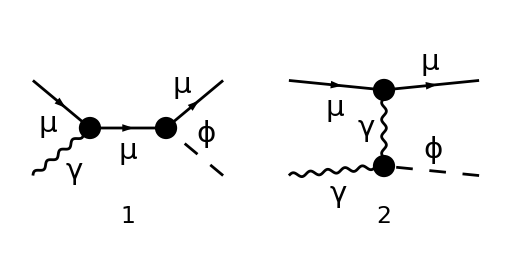

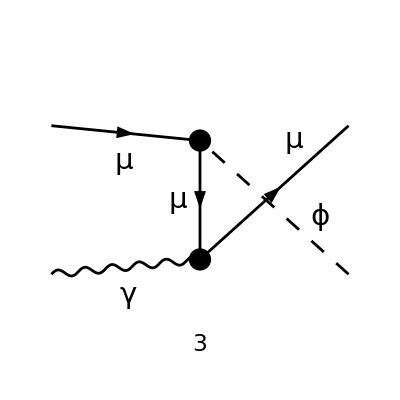

```mathematica
diagrams2to2= InsertFields[CreateTopologies[0, 2 -> 2], {F[2],V[1]} ->
		{F[2],S[1]}, InsertionLevel -> {Classes}, Model->"pseudoscalar_mubeamdump"];
Paint[diagrams2to2, ColumnsXRows -> {2, 1}, Numbering -> Simple,
	SheetHeader->None,ImageSize->{512,256}];
```

```mathematica
amplitude=FCFAConvert[CreateFeynAmp[diagrams2to2], IncomingMomenta->{p,q},
	OutgoingMomenta->{pprime,k},UndoChiralSplittings->True,ChangeDimension->4,
	TransversePolarizationVectors->{q}, List->False, SMP->True,
	Contract->True];
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

in total: 3 Classes amplitudes

```mathematica
amplitude
```

(ⅈ e (φ(OverBar[p'],m_μ)).(ⅈ y_μ (γ̄)^6-ⅈ y_μ (γ̄)^7).(γ̄·(k̄+OverBar[p'])+m_μ).(γ̄·ε̄(q)).(φ(p̄,m_μ)))/((-k̄-OverBar[p'])^2-m_μ^2)+(ⅈ e (φ(OverBar[p'],m_μ)).(γ̄·ε̄(q)).(γ̄·(OverBar[p']-q̄)+m_μ).(ⅈ y_μ (γ̄)^6-ⅈ y_μ (γ̄)^7).(φ(p̄,m_μ)))/((q̄-OverBar[p'])^2-m_μ^2)+(8 e g_P (φ(OverBar[p'],m_μ)).(γ̄·ε̄(q)).(φ(p̄,m_μ)))/(k̄-q̄)^2

FeynArts → FeynRules → FeynArts is not correctly calculating the Primakoff piece of the amplitude, so I calculate it by hand:

```mathematica
DiracTrace[GA[μ, ν, ρ, σ,5]/4I, DiracTraceEvaluate->True]
```

(ϵ̄)^μνρσ

```mathematica
DiracTrace[GA[μ, ν, 5,ρ,5, σ], DiracTraceEvaluate->True]
```

-4 ((ḡ)^μσ (ḡ)^νρ-(ḡ)^μρ (ḡ)^νσ+(ḡ)^μν (ḡ)^ρσ)

```mathematica
DiracTrace[GA[μ1, ν1, ρ1, σ1,5]/4I, DiracTraceEvaluate->True]*
DiracTrace[GA[μ2, ν2, ρ2, σ2,5]/4I, DiracTraceEvaluate->True]*
MetricTensor[μ1,μ2]*
FourVector[k-q,ν1]FourVector[q,σ1]*
FourVector[k-q,ν2]FourVector[q,σ2]*
DiracTrace[DiracSlash[pprime].GA[ρ1,5].DiracSlash[p].GA[5,ρ2], DiracTraceEvaluate->True]
```

2 (q̄)^σ1 (q̄)^σ2 (ḡ)^μ1μ2 (k̄-q̄)^ν1 (k̄-q̄)^ν2 (ϵ̄)^μ1ν1ρ1σ1 (ϵ̄)^μ2ν2ρ2σ2 (2 m_μ^2 (ḡ)^ρ1ρ2-t_2 (ḡ)^ρ1ρ2-2 OverBar[p']^ρ1 (p̄)^ρ2-2 OverBar[p']^ρ2 (p̄)^ρ1)

```mathematica
(1/2)^2((8e gPrimakoff)^2/(Contract[FourVector[k-q,μ]FourVector[k-q,μ]])^2)Contract[DiracTrace[GA[μ1, ν1, ρ1, σ1,5]/4I, DiracTraceEvaluate->True]*
DiracTrace[GA[μ2, ν2, ρ2, σ2,5]/4I, DiracTraceEvaluate->True]*
MetricTensor[μ1,μ2]*
FourVector[k-q,ν1]FourVector[q,σ1]*
FourVector[k-q,ν2]FourVector[q,σ2]*
DiracTrace[DiracSlash[pprime].GA[ρ1,5].DiracSlash[p].GA[5,ρ2], DiracTraceEvaluate->True]]//
TrickMandelstam[#,{s2,t2,u2,q^2+2 mmu^2+mBSM^2}]&//FullSimplify
```

-(16 e^2 g_P^2 (-2 q^2 m_ϕ^2+2 m_μ^4-2 m_μ^2 (s_2+u_2)+s_2^2+u_2^2))/t_2

```mathematica
PrimakoffAmplitudeSquared=(1/2)^2((4e gPrimakoff)^2/(Contract[FourVector[k-q,μ]FourVector[k-q,μ]])^2)Contract[DiracTrace[GA[μ1, ν1, ρ1, σ1,5]/4I, DiracTraceEvaluate->True]*
DiracTrace[GA[μ2, ν2, ρ2, σ2,5]/4I, DiracTraceEvaluate->True]*
MetricTensor[μ1,μ2]*
FourVector[k-q,ν1]FourVector[q,σ1]*
FourVector[k-q,ν2]FourVector[q,σ2]*
DiracTrace[DiracSlash[pprime].GA[ρ1,5].DiracSlash[p].GA[5,ρ2], DiracTraceEvaluate->True]]//.{SP[q,q]->0,q^4->0}//.{t2->mBSM^2+2 mmu^2-s2-u2} //FullSimplify
```

-(4 e^2 g_P^2 (2 m_μ^4-2 m_μ^2 (s_2+u_2)+s_2^2+u_2^2))/(2 m_μ^2+m_ϕ^2-s_2-u_2)

```mathematica
PrimakoffAmplitudeSquared//.TwoToTildeMu//FullSimplify
```

-(4 e^2 g_P^2 ((s̃)^2+(ũ)^2))/(-s̃-ũ+m_ϕ^2)

```mathematica
PrimakoffAmplitudeSquared//.TwoToTildeMu//.{stilde->-utilde/(1-x)}//FullSimplify
```

(4 e^2 (ũ)^2 g_P^2 ((x-2) x+2))/((x-1) (ũ x-m_ϕ^2 (x-1)))

```mathematica
PrimakoffA2to2 = PrimakoffAmplitudeSquared/(e gPrimakoff)^2//.TwoToTildeMu//FullSimplify
```

(4 ((s̃)^2+(ũ)^2))/(s̃+ũ-m_ϕ^2)

```mathematica
PrimakoffA2to2//.{SP[q,q]->0,q^4->0}//.{t2->SP[q,q]+mBSM^2+2 mmu^2-s2-u2}//.{SP[q,q]->0,q^4->0}//.TwoToTildeMu //.{stilde->-utilde/(1-x)}//FullSimplify
```

(4 (ũ)^2 ((x-2) x+2))/((x-1) (ũ x-m_ϕ^2 (x-1)))

```mathematica
PrimakoffA2to2//.{SP[q,q]->0,q^4->0}//.{t2->SP[q,q]+mBSM^2+2 mmu^2-s2-u2}//.{SP[q,q]->0,q^4->0}//.TwoToTildeMu //.tMinApproximations//FullSimplify
```

-(4 ((x-2) x+2) (m_ϕ^2 (x-1)-x^2 (E_0^2 θ_ϕ^2+m_μ^2))^2)/((x-1) x^4 (E_0^2 θ_ϕ^2+m_μ^2))

The rest of the amplitude is calculated correctly, however:

```mathematica
(* amplitudeSquared = (amplitude (ComplexConjugate[amplitude]))//
FeynAmpDenominatorExplicit//
DoPolarizationSums[#,q,0]&//
(*DoPolarizationSums[#,k,0]&// (* Only for spin 1 *) *)
FermionSpinSum[#, ExtraFactor -> 1/2^2 (* Averaging over initial lepton and photon pols *)]&//
DiracSimplify//
TrickMandelstam[#,{s2,t2,u2,q^2+2 mmu^2+mBSM^2}]&//
FullSimplify; *)
```

PolarizationSum::notmassless: Warning! You are inserting a polarization sum for massless vector bosons, but the momentum of the external boson q is not on-shell. Please put it on-shell via ScalarProduct[q,q]=0

Adding the manually calculated Primakoff result to the rest of the amplitude squared.

The γ^5 structure of the amplitude prevents interference between these terms.

```mathematica
amplitudeSquared = (
PrimakoffAmplitudeSquared +
(amplitude (ComplexConjugate[amplitude]))//
FeynAmpDenominatorExplicit//
DoPolarizationSums[#,q,0]&//
(*DoPolarizationSums[#,k,0]&// (* Only for spin 1 *) *)
FermionSpinSum[#, ExtraFactor -> 1/2^2 (* Averaging over initial lepton and photon pols *)]&//
DiracSimplify//
TrickMandelstam[#,{s2,t2,u2,q^2+2 mmu^2+mBSM^2}]&/.gPrimakoff->0)//
FullSimplify;
```

PolarizationSum::notmassless: Warning! You are inserting a polarization sum for massless vector bosons, but the momentum of the external boson q is not on-shell. Please put it on-shell via ScalarProduct[q,q]=0

```mathematica
amplitudeSquared
```

e^2 (1/((m_μ^2-s_2)^2 (m_μ^2-u_2)^2)y_μ^2 (m_ϕ^2 (2 m_μ^4 (q^2-s_2-u_2)-2 m_μ^2 (q^2 (s_2+u_2)+2 s_2 u_2)+q^2 (s_2^2+u_2^2)+4 m_μ^6+2 s_2 u_2 (s_2+u_2))-2 m_ϕ^4 (m_μ^2-s_2) (m_μ^2-u_2)-(m_μ^2-s_2) (m_μ^2-u_2) (-2 m_μ^2+s_2+u_2)^2)+1/(t_2^2 (q^2-t_2))2 g_P^2 (2 m_μ^2 (q^2 (t_2^2-32)+t_2 (t_2 (m_ϕ^2-t_2-2 u_2)+32))+t_2 (q^4 t_2-2 q^2 (t_2 (-m_ϕ^2+t_2+u_2)+16)+t_2 (m_ϕ^4-2 m_ϕ^2 (t_2+u_2)+t_2^2+2 t_2 u_2+2 u_2^2+32))+2 m_μ^4 t_2^2))

### Applying Standard Formula for dσ/dt_2 in the Lab Frame

#### Setting up 2→2 Differential Cross Sections

Off-Shell

```mathematica
var["dσ/dt_2"] = amplitudeSquared/(16π stilde^2)//.BeamDumpCouplingRules//.TwoToTildeMu//TrickMandelstam[#,{stilde,t2,utilde,q^2+mBSM^2}]&//FullSimplify;
var["dσ/(d (p . k))"] = 2var["dσ/dt_2"]//FullSimplify;
var["A^(2 → 2)"]=(stilde^2 var["dσ/(d (p . k))"])/(2π epsmu^2 alphaEM^2)//FullSimplify;
```

On-Shell

```mathematica
var["dσ/(d (p . k)) on-shell"] = var["dσ/(d (p . k))"]/.q^2->0//FullSimplify;
var["A^(2 → 2) on-shell"]=(stilde^2 var["dσ/(d (p . k)) on-shell"])/(2π epsmu^2 alphaEM^2)//FullSimplify;
```

#### Explicit Expressions

Off-shell

```mathematica
Print["dσ/dt_2 = "TraditionalForm[var["dσ/dt_2"] ]]
Print["dσ/(d (p . k)) = "TraditionalForm[var["dσ/(d (p . k))"]]]
Print["A^(2 → 2) = "TraditionalForm[var["A^(2 → 2)"]]]
```

dσ/dt_2 =  (α_EM^2 π ((ϵ_μ^2 (-2 s̃ ũ m_ϕ^4+(((s̃)^2+(ũ)^2) q^2+2 m_μ^2 (s̃+ũ)^2+2 s̃ ũ (s̃+ũ)) m_ϕ^2-s̃ ũ (s̃+ũ)^2))/(ũ)^2-(2 ϵ_P^2 (s̃)^2 (64 (q^2-t_2) m_μ^2+t_2 (-((s̃)^2+(ũ)^2+32) m_ϕ^2+32 (s̃+ũ)-(q^2-s̃-ũ) ((s̃)^2+(ũ)^2))))/((q^2-t_2) t_2^2)))/(s̃)^4

dσ/(d (p . k)) =  1/(s̃)^4 2 α_EM^2 π ((ϵ_μ^2 (-2 s̃ ũ m_ϕ^4+(((s̃)^2+(ũ)^2) q^2+2 m_μ^2 (s̃+ũ)^2+2 s̃ ũ (s̃+ũ)) m_ϕ^2-s̃ ũ (s̃+ũ)^2))/(ũ)^2-(2 ϵ_P^2 (s̃)^2 (64 (q^2-t_2) m_μ^2+t_2 (-((s̃)^2+(ũ)^2+32) m_ϕ^2+32 (s̃+ũ)-(q^2-s̃-ũ) ((s̃)^2+(ũ)^2))))/((q^2-t_2) t_2^2))

A^(2 → 2) =  ((-2 s̃ ũ m_ϕ^4+(((s̃)^2+(ũ)^2) q^2+2 m_μ^2 (s̃+ũ)^2+2 s̃ ũ (s̃+ũ)) m_ϕ^2-s̃ ũ (s̃+ũ)^2)/((s̃)^2 (ũ)^2)-(2 ϵ_P^2 (64 (q^2-t_2) m_μ^2+t_2 (-((s̃)^2+(ũ)^2+32) m_ϕ^2+32 (s̃+ũ)-(q^2-s̃-ũ) ((s̃)^2+(ũ)^2))))/(ϵ_μ^2 (q^2-t_2) t_2^2))

On-shell

```mathematica
Print["(FractionBox[dσ, d (p . k)])_(on - shell) = "TraditionalForm[var["dσ/(d (p . k)) on-shell"] ]]
Print["(SuperscriptBox[A, 2 → 2])_(.00on - shell) = "TraditionalForm[var["A^(2 → 2) on-shell"]]]
```

(FractionBox[dσ, d (p . k)])_(on - shell) =  (2 α_EM^2 π (((-2 s̃ ũ m_ϕ^4+2 (s̃+ũ) ((s̃+ũ) m_μ^2+s̃ ũ) m_ϕ^2-s̃ ũ (s̃+ũ)^2) ϵ_μ^2)/(ũ)^2+(2 ϵ_P^2 (s̃)^2 (-((s̃)^2+(ũ)^2+32) m_ϕ^2-64 m_μ^2+(s̃+ũ) ((s̃)^2+(ũ)^2+32)))/t_2^2))/(s̃)^4

(SuperscriptBox[A, 2 → 2])_(.00on - shell) =  ((2 (-((s̃)^2+(ũ)^2+32) m_ϕ^2-64 m_μ^2+(s̃+ũ) ((s̃)^2+(ũ)^2+32)) ϵ_P^2)/(ϵ_μ^2 t_2^2)+(-2 s̃ ũ m_ϕ^4+2 (s̃+ũ) ((s̃+ũ) m_μ^2+s̃ ũ) m_ϕ^2-s̃ ũ (s̃+ũ)^2)/((s̃)^2 (ũ)^2))

### Applying Kinematic Approximations

#### Stating Approximations:

```mathematica
tMinApproximations = {
stilde->-utilde/(1-x),
utilde->-x E0^2 thetaBSM^2-mBSM^2(1-x)/x-mmu^2 x,
t2->(utilde x)/(1-x)+mBSM^2,
SP[q,q]->-stilde^2/(4 E0^2)
};
```

```mathematica
tMinApproximations2 = {
stilde->-utilde/(1-x),
t2->(utilde x)/(1-x)+mBSM^2,
SP[q,q]->-stilde^2/(4 E0^2)
};
```

#### Applying Approximations

Off-shell

```mathematica
var["dσ/(d (p . k)) near tmin"] =var["dσ/(d (p . k))"]//.tMinApproximations//FullSimplify;
```

```mathematica
var["A^(2 → 2) near tmin"]=(stilde^2 var["dσ/(d (p . k)) near tmin"])/(2π epsmu^2 alphaEM^2)//.tMinApproximations//FullSimplify;
```

On-shell

```mathematica
var["dσ/(d (p . k)) on-shell near tmin"] =var["dσ/(d (p . k)) on-shell"]//.tMinApproximations//FullSimplify;
```

```mathematica
var["A^(2 → 2) on-shell near tmin"]=(stilde^2 var["dσ/(d (p . k)) on-shell near tmin"])/(2π epsmu^2 alphaEM^2)//.tMinApproximations//FullSimplify;
```

```mathematica
var["dσ/(d (p . k)) on-shell"]/.BeamDumpCouplingRules//.tMinApproximations2//FullSimplify
```

1/((ũ)^6 (1-x))2 π (α_EM-α_EM x)^2 (ũ ϵ_μ^2 ((ũ)^3 x^2-2 ũ m_ϕ^2 (x-1) x (ũ+m_μ^2 x)+2 ũ m_ϕ^4 (x-1)^2)+(2 (ũ)^4 ϵ_P^2 ((ũ)^3 (-x) ((x-2) x+2)+m_ϕ^2 (x-1) ((ũ)^2 ((x-2) x+2)+32 (x-1)^2)-32 ũ (x-1)^2 x+64 m_μ^2 (x-1)^3))/((m_ϕ^2 (x-1)-ũ x)^2))

```mathematica
var["dσ/(d (p . k)) on-shell"]/.BeamDumpCouplingRules//.tMinApproximations2/.epsmu->0//FullSimplify
```

(4 π α_EM^2 ϵ_P^2 (x-1) ((ũ)^3 x ((x-2) x+2)-m_ϕ^2 (x-1) ((ũ)^2 ((x-2) x+2)+32 (x-1)^2)+32 ũ (x-1)^2 x-64 m_μ^2 (x-1)^3))/((ũ)^2 (m_ϕ^2 (x-1)-ũ x)^2)

```mathematica
amplitudeSquared/(e^2 gPrimakoff^2)/.BeamDumpCouplingRules//.tMinApproximations2/.epsmu->0//FullSimplify
```

(2 (((ũ x)/(1-x)+m_ϕ^2) (((ũ)^2 (((ũ x)/(1-x)+m_ϕ^2) ((ũ x)/(1-x)+u_2)+16))/(2 (E_0-E_0 x)^2)+((m_ϕ^2 (x-1)-ũ x) (x (((ũ)^2+32) x-64)-2 ũ u_2 x (x-1)+2 u_2^2 (x-1)^2+32))/(x-1)^3+q^4 ((ũ x)/(1-x)+m_ϕ^2))+2 m_μ^2 (((ũ x)/(1-x)+m_ϕ^2) (((m_ϕ^2 (x-1)-ũ x) (ũ x-2 u_2 (x-1)))/(x-1)^2+32)-((ũ)^2 (((ũ x)/(1-x)+m_ϕ^2)^2-32))/(4 (E_0-E_0 x)^2))+2 m_μ^4 ((ũ x)/(1-x)+m_ϕ^2)^2))/(((ũ x)/(1-x)+m_ϕ^2)^2 ((ũ (4 (x-1) x-(ũ)/E_0^2))/(4 (x-1)^2)-m_ϕ^2))

#### Explicit Expressions

Off-Shell

```mathematica
var["dσ/(d (p . k)) near tmin"]
```

(π (α_EM-α_EM x)^2 (ϵ_μ^2 x^2 (-(m_ϕ^2 ((x-2) x+2) (m_ϕ^2 (x-1)-x^2 (E_0^2 θ_ϕ^2+m_μ^2))^4)/E_0^2-8 m_ϕ^2 (x-1)^2 x^2 (x^2 (E_0^2 θ_ϕ^2+m_μ^2)-m_ϕ^2 (x-1))^3-4 (x-1) x^2 (m_ϕ^2 (x-1)-x^2 (E_0^2 θ_ϕ^2+m_μ^2))^4+8 m_μ^2 m_ϕ^2 (x-1)^2 x^2 (m_ϕ^2 (x-1) x-x^3 (E_0^2 θ_ϕ^2+m_μ^2))^2-8 m_ϕ^4 (x-1)^3 (m_ϕ^2 (x-1) x-x^3 (E_0^2 θ_ϕ^2+m_μ^2))^2)-(8 ϵ_P^2 (1-x) (m_ϕ^2 (x-1)-x^2 (E_0^2 θ_ϕ^2+m_μ^2))^4 (64 m_μ^2 (1-x)^3 (x^4 (E_0^2 θ_ϕ^2+m_μ^2) (E_0^2 (θ_ϕ^2+4 x-4)+m_μ^2)-2 m_ϕ^2 (x-1) x^2 (E_0^2 θ_ϕ^2+m_μ^2)+m_ϕ^4 (x-1)^2)+(E_0^2 θ_ϕ^2+m_μ^2) (-128 E_0^2 (x-1)^3 x^3 (x^3 (E_0^2 θ_ϕ^2+m_μ^2)-m_ϕ^2 (x-1) x)-4 E_0^2 m_ϕ^2 (x-1)^2 x^2 ((x-1)^2 (m_ϕ^2 (x-1)-x^2 (E_0^2 θ_ϕ^2+m_μ^2))^2+(m_ϕ^2 (x-1)-x^2 (E_0^2 θ_ϕ^2+m_μ^2))^2+32 (x-1)^2 x^2)-((x-2) x+2) (m_ϕ^2 (x-1)-x^2 (E_0^2 θ_ϕ^2+m_μ^2))^2 (-x^4 (E_0^2 θ_ϕ^2+m_μ^2) (E_0^2 (θ_ϕ^2-4 x+4)+m_μ^2)+2 m_ϕ^2 (x-1) x^2 (E_0^2 (θ_ϕ^2-2 x+2)+m_μ^2)+m_ϕ^4 (-(x-1)^2)))))/(x^2 (E_0^2 θ_ϕ^2+m_μ^2)^2 (x^4 (E_0^2 θ_ϕ^2+m_μ^2) (E_0^2 (θ_ϕ^2+4 x-4)+m_μ^2)-2 m_ϕ^2 (x-1) x^2 (E_0^2 θ_ϕ^2+m_μ^2)+m_ϕ^4 (x-1)^2))))/(2 (x-1)^2 (m_ϕ^2 (x-1)-x^2 (E_0^2 θ_ϕ^2+m_μ^2))^6)

```mathematica
var["A^(2 → 2) near tmin"]
```

-1/(4 (x-1)^2)((8 ϵ_P^2 (1-x) (64 m_μ^2 (1-x)^3 (x^4 (E_0^2 θ_ϕ^2+m_μ^2) (E_0^2 (θ_ϕ^2+4 x-4)+m_μ^2)-2 m_ϕ^2 (x-1) x^2 (E_0^2 θ_ϕ^2+m_μ^2)+m_ϕ^4 (x-1)^2)+(E_0^2 θ_ϕ^2+m_μ^2) (-128 E_0^2 (x-1)^3 x^3 (x^3 (E_0^2 θ_ϕ^2+m_μ^2)-m_ϕ^2 (x-1) x)-4 E_0^2 m_ϕ^2 (x-1)^2 x^2 ((x-1)^2 (m_ϕ^2 (x-1)-x^2 (E_0^2 θ_ϕ^2+m_μ^2))^2+(m_ϕ^2 (x-1)-x^2 (E_0^2 θ_ϕ^2+m_μ^2))^2+32 (x-1)^2 x^2)-((x-2) x+2) (m_ϕ^2 (x-1)-x^2 (E_0^2 θ_ϕ^2+m_μ^2))^2 (-x^4 (E_0^2 θ_ϕ^2+m_μ^2) (E_0^2 (θ_ϕ^2-4 x+4)+m_μ^2)+2 m_ϕ^2 (x-1) x^2 (E_0^2 (θ_ϕ^2-2 x+2)+m_μ^2)+m_ϕ^4 (-(x-1)^2)))))/(ϵ_μ^2 x^4 (E_0^2 θ_ϕ^2+m_μ^2)^2 (x^4 (E_0^2 θ_ϕ^2+m_μ^2) (E_0^2 (θ_ϕ^2+4 x-4)+m_μ^2)-2 m_ϕ^2 (x-1) x^2 (E_0^2 θ_ϕ^2+m_μ^2)+m_ϕ^4 (x-1)^2))+(4 E_0^2 (x-1) x^6 (E_0^2 θ_ϕ^2+m_μ^2)^2-2 m_ϕ^4 (x-1) x^2 (E_0^2 (θ_ϕ^2 ((x-2) x+2)-2 (x-1)^2)+m_μ^2 ((x-2) x+2))+m_ϕ^2 x^4 (E_0^4 θ_ϕ^4 ((x-2) x+2)+2 E_0^2 m_μ^2 (θ_ϕ^2 ((x-2) x+2)-4 (x-1)^2)+m_μ^4 ((x-2) x+2))+m_ϕ^6 (x-1)^2 ((x-2) x+2))/(E_0^2 (m_ϕ^2 (x-1)-x^2 (E_0^2 θ_ϕ^2+m_μ^2))^2))

On-shell

```mathematica
var["dσ/(d (p . k)) on-shell near tmin"]
```

(2 π (α_EM-α_EM x)^2 (ϵ_μ^2 x^3 (m_ϕ^2 (x-1) x-x^3 (E_0^2 θ_ϕ^2+m_μ^2))^2 (x^4 (E_0^2 θ_ϕ^2+m_μ^2)^2-2 m_μ^2 m_ϕ^2 (x-1) x^2+m_ϕ^4 (x-1)^2)+1/(x (E_0^2 θ_ϕ^2+m_μ^2)^2)2 ϵ_P^2 (m_μ^4 x^2 ((x-2) x+2) (3 E_0^2 θ_ϕ^2 x^2-2 m_ϕ^2 (x-1))+m_μ^2 (x (3 E_0^4 θ_ϕ^4 x^5-6 E_0^4 θ_ϕ^4 x^4+x^3 (6 E_0^4 θ_ϕ^4+32)-160 x+192)-4 E_0^2 θ_ϕ^2 m_ϕ^2 (x-1) x^2 ((x-2) x+2)+m_ϕ^4 (x-1)^2 ((x-2) x+2)-64)+E_0^2 θ_ϕ^2 (x^2 (x (x (E_0^4 θ_ϕ^4 ((x-2) x+2)+32)-64)+32)-2 E_0^2 θ_ϕ^2 m_ϕ^2 (x-1) x^2 ((x-2) x+2)+m_ϕ^4 (x-1)^2 ((x-2) x+2))+m_μ^6 x^4 ((x-2) x+2)) (m_ϕ^2 (x-1)-x^2 (E_0^2 θ_ϕ^2+m_μ^2))^4))/((1-x) x^7 ((m_ϕ^2 (x-1))/x-x (E_0^2 θ_ϕ^2+m_μ^2))^6)

```mathematica
var["A^(2 → 2) on-shell near tmin"]//FullSimplify
```

((x-1)^2 (m_ϕ^2 (x-1)-x^2 (E_0^2 θ_ϕ^2+m_μ^2))^2 (ϵ_μ^2 x^3 (m_ϕ^2 (x-1) x-x^3 (E_0^2 θ_ϕ^2+m_μ^2))^2 (x^4 (E_0^2 θ_ϕ^2+m_μ^2)^2-2 m_μ^2 m_ϕ^2 (x-1) x^2+m_ϕ^4 (x-1)^2)+1/(x (E_0^2 θ_ϕ^2+m_μ^2)^2)2 ϵ_P^2 (m_μ^4 x^2 ((x-2) x+2) (3 E_0^2 θ_ϕ^2 x^2-2 m_ϕ^2 (x-1))+m_μ^2 (x (3 E_0^4 θ_ϕ^4 x^5-6 E_0^4 θ_ϕ^4 x^4+x^3 (6 E_0^4 θ_ϕ^4+32)-160 x+192)-4 E_0^2 θ_ϕ^2 m_ϕ^2 (x-1) x^2 ((x-2) x+2)+m_ϕ^4 (x-1)^2 ((x-2) x+2)-64)+E_0^2 θ_ϕ^2 (x^2 (x (x (E_0^4 θ_ϕ^4 ((x-2) x+2)+32)-64)+32)-2 E_0^2 θ_ϕ^2 m_ϕ^2 (x-1) x^2 ((x-2) x+2)+m_ϕ^4 (x-1)^2 ((x-2) x+2))+m_μ^6 x^4 ((x-2) x+2)) (m_ϕ^2 (x-1)-x^2 (E_0^2 θ_ϕ^2+m_μ^2))^4))/(ϵ_μ^2 (1-x)^3 x^9 ((m_ϕ^2 (x-1))/x-x (E_0^2 θ_ϕ^2+m_μ^2))^6)

```mathematica
PrimakoffA2to2//.tMinApproximations//FullSimplify
```

-(4 ((x-2) x+2) (m_ϕ^2 (x-1)-x^2 (E_0^2 θ_ϕ^2+m_μ^2))^2)/((x-1) x^4 (E_0^2 θ_ϕ^2+m_μ^2))

# Saving Results

Putting everything into a single function

```mathematica
var["Squared, Spin-Averaged Matrix Element"]=amplitudeSquared;
var["Squared, Spin-Averaged Matrix Element on-shell"]=amplitudeSquared//.SP[q,q]->0;
```

```mathematica
keys = {"Squared, Spin-Averaged Matrix Element",
"Squared, Spin-Averaged Matrix Element on-shell",
"dσ/(d (p . k))", "dσ/(d (p . k)) on-shell",
"dσ/(d (p . k)) near tmin", "dσ/(d (p . k)) on-shell near tmin",
"A^(2 → 2)", "A^(2 → 2) on-shell",
"A^(2 → 2) near tmin", "A^(2 → 2) on-shell near tmin"};
```

```mathematica
Do[pseudoscalar2to2[keys[[i]]]=var[keys[[i]]],{i,Length[keys]}]

(* For debugging: *)
(*pseudoscalar2to2/@keys*)
```

Saving all functions

```mathematica
Put[FullDefinition[pseudoscalar2to2],$pseudoscalar2to2Functions]
```

```mathematica
PutAppend[FullDefinition[tMinApproximations], $pseudoscalar2to2Functions]
```

```mathematica
Quit[]
```